## Problem 1

```mathematica
f[x_]:=E^(Sqrt[5]x)-13.5 * Cos[0.1 x] + 25 x^4
df[x_]:=√5 ⅇ^(√5 x)+100 x^3+1.35 Sin[0.1 x]
```

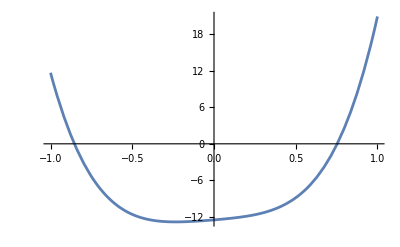

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
FindRoot[f[x],{x,0}]
```

{x→0.753701}

## Problem 2

```mathematica
f[x_]:= x Cos[x] - Sin[x]
```

```mathematica
f'[x]
```

-x Sin[x]

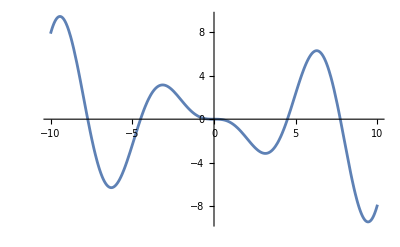

```mathematica
Plot[f[x],{x,-10,10}]
```

```mathematica
Root[f[x],{x,4,5}]
```

Root::nup: x Cos[x]-Sin[x] is not a univariate polynomial.

Root[x Cos[x]-Sin[x],{x,4,5}]

## Problem 3

```mathematica
f[x_,y_]:= x y - 0.1
g[x_,y_]:= x^2 + 3 y^2 -2
```

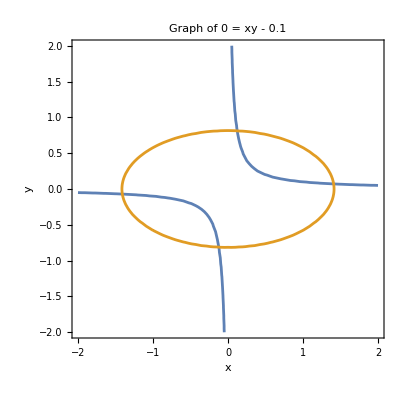

```mathematica
ContourPlot[{x y-0.1==0, x^2 + 3 y^2 -2 == 0},{x,-2,2},{y,-2,2},Contours->{0},PlotRange->All,AxesLabel->{"x","y"},PlotLabel->"Graph of 0 = xy - 0.1",Mesh->None,PlotStyle->Thick]
```

```mathematica
Solve[{x y - 0.1 ==0, x^2 + 3 y^2 -2 == 0}, {x,y}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-1.40886,y→-0.0709794},{x→-0.12294,y→-0.813406},{x→0.12294,y→0.813406},{x→1.40886,y→0.0709794}}